```mathematica
BASEHEALTH=85;
(*This function generates a Matrix of values so that the algorithm knows which values are coming for a given iteration. *)
MakeHarvestProfile :=Module[{harvestProfile},
harvestProfile=Table[
harvestNum=RandomReal[{0,1}];
Which[
harvestNum≤0.18,
6,
harvestNum≤0.4,
13,
harvestNum≤0.69,
10,
harvestNum≤1,
8
],{x,9},{y,10}];
Return[harvestProfile];
];
```

```mathematica
(*This statement creates and sets a global variable for the harvest of a given run.*)
(*harvestProfile=MakeHarvestProfile;*)

(*Below are the functions for LifeEnjoyment given health and investment, Health Regained given an investment, and Health Degeneration per round.
Each is preceded by its associated constants.*)
alpha=0.028;
beta = 0.5;
mu=0.5;
c=500;
LifeEnjoyment[investment_,currentHealth_]:= c*(beta*(currentHealth/100)+mu)*(1-E^((-1)*alpha*investment));
r = 0;
gamma = 30;
sigma = 0.025;
HealthRegained[investment_]:=gamma*((1-E^((-1)*sigma*investment))/(1+E^((-1)*sigma*(investment-r))));
HealthDegeneration[currentHealth_,currentRound_]:=currentHealth-(15+currentRound);
```

```mathematica
(*Given the current round and current health, this function evaluates the current harvestProfile and returns the effective harvest of a round.
It should be noted that the current health and current round can be adjusted in this function without affecting the harvestProfile*)
HarvestCurrentRound[currentHealth_,currentRound_]:=
Module[{currentHarvest,harvestTimer,evHarvest},
(*harvestTimer=Which[
currentHealth>0,
Floor[30*(currentHealth/100)/3],
currentHealth≤0,
0];*)
evHarvest=9.32;
If[currentHealth≥0,
currentHarvest=10*evHarvest*(currentHealth/100)(*Total[harvestProfile[[currentRound]][[1;;harvestTimer]]]*),
currentHarvest=0];
Return[currentHarvest]
];
```

```mathematica
CalculateRandomSpendingProfile:=
healthValues = RandomChoice[Range[0,1,0.001],9];

HealthSpendingPerRound[healthSpendingStrategy_,BASEHEALTH_]:=
Module[{healthPerRoundWithSpending,currentHarvest,health},
health=BASEHEALTH;
healthPerRoundWithSpending = Table[
If[HealthDegeneration[health,i]>0,
currentHarvest = HarvestCurrentRound[health,i],
currentHarvest=0];
If[health>0&&currentHarvest>0,
health = Min[HealthDegeneration[health,i]+HealthRegained[healthSpendingStrategy[[i]]*currentHarvest],100],
health=0
]
,{i,1,Length[healthSpendingStrategy]}];
Return[healthPerRoundWithSpending]
];

LifeEnjoymentSpendingPerRound[lifeEnjoymentSpendingStrategy_,health_]:=
Module[{currentHarvest,lifeEnjoyment,lifeEnjoymentPerRoundWithSpending},
lifeEnjoyment=0;
currentHarvest=0;
lifeEnjoymentPerRoundWithSpending = Table[
If[health[[i]]>0,
currentHarvest = HarvestCurrentRound[health[[i]],i],
currentHarvest=0];
lifeEnjoyment+=LifeEnjoyment[lifeEnjoymentSpendingStrategy[[i]]*currentHarvest,health[[i]]]
,{i,1,Length[lifeEnjoymentSpendingStrategy]}
];
Return[lifeEnjoymentPerRoundWithSpending]
];

SpendingPerRound[healthSpendingStrategy_,BASEHEALTH_]:=
Module[{currentHarvest,lifeEnjoymentSpendingProfile,lifeEnjoyment,health},
lifeEnjoymentSpendingProfile = 1-healthSpendingStrategy;
health = HealthSpendingPerRound[healthSpendingStrategy,BASEHEALTH];
lifeEnjoyment = LifeEnjoymentSpendingPerRound[lifeEnjoymentSpendingProfile,health];
Return[Transpose[{health,lifeEnjoyment}]]
];
```

```mathematica
MutationDistribution=TruncatedDistribution[{0,1},NormalDistribution[μ,σ]];
Mutation[healthSpendingStrategy_,mutationDeviation_]:=
Module[{chanceOfMutation,newSpendingStrat,inputStrategy},
inputStrategy=healthSpendingStrategy;
newSpendingStrat=Table[
chanceOfMutation=RandomReal[{0,1}];
Which[
chanceOfMutation≤0.1,
inputStrategy[[i]]=RandomVariate[MutationDistribution/.{μ->inputStrategy[[i]],σ->mutationDeviation[[i]]}],
chanceOfMutation>0.1,
inputStrategy[[i]]
]
,{i,1,Length[healthSpendingStrategy]}
];
Return[newSpendingStrat]
];
```

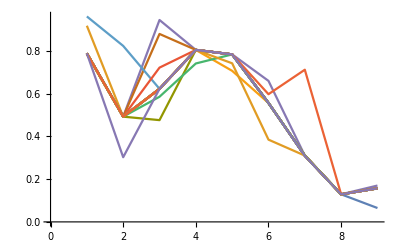

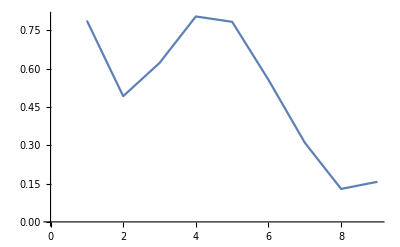

```mathematica
test =CalculateRandomSpendingProfile;
mutatedProfiles = Table[
Mutation[test,{.3,.3,.3,.3,.3,.3,.3,.3,.3}]
,{20}];
ListLinePlot[mutatedProfiles]
ListLinePlot[test]
```

# Simluation

#### Contains tournament selection and implementation specifics not covered in functions.

```mathematica
(*n is the number of profiles generated*)
populationSize=1000;
generations=10;
(*Allocate and Populate the two arrays for populations. One is the initial which is perpetuated, the second is a storage array
which stores the values to be passed on during computation*)
best={0,0,0,0,0,0,0,0,0};
initialProfilePopulation=Table[
CalculateRandomSpendingProfile,
{populationSize}];
resultingPopulation=ConstantArray[0,populationSize];
(*Randomly Select 2 profiles from the population of profiles, and evaluate their corresponding health and payout profiles*)
Do[
mutability=StandardDeviation[initialProfilePopulation];
Do[
profileOne =RandomChoice[initialProfilePopulation];
profileTwo =RandomChoice[initialProfilePopulation];
spendingOne=SpendingPerRound[profileOne,BASEHEALTH];
spendingTwo=SpendingPerRound[profileTwo,BASEHEALTH];

(*Tournament Selection. Randomly Select 2 Health Spending profiles, pass on the more fit profile*)
resultingPopulation[[j]]=
Which[
spendingOne[[9]][[2]]≥spendingTwo[[9]][[2]],
Mutation[profileOne,mutability],
spendingOne[[9]][[2]]≤spendingTwo[[9]][[2]],
Mutation[profileTwo,mutability]
];
(*If a specific profile is better than the current best observed profile, store it as the new best profile*)
If[spendingOne[[9]][[2]]>SpendingPerRound[best,BASEHEALTH][[9]][[2]],
best=profileOne;
];
If[spendingTwo[[9]][[2]]>SpendingPerRound[best,BASEHEALTH][[9]][[2]],
best=profileTwo;
];
,{j,1,populationSize}
];
initialProfilePopulation=resultingPopulation;,
{generations}
];
```

(89.812 | 129.892
92.0127 | 362.105
94.0634 | 582.319
92.7063 | 873.93
91.675 | 1124.86
86.6448 | 1420.64
79.6688 | 1695.31
69.648 | 1948.81
52.5592 | 2186.36)

{0.863538,0.724653,0.75355,0.615742,0.69,0.555597,0.545242,0.499,0.28911}

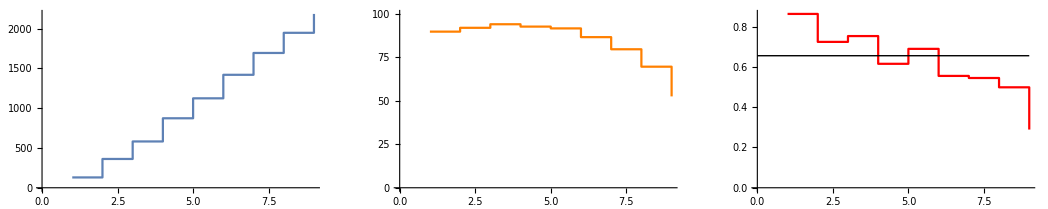

```mathematica
Text[Style[SpendingPerRound[best,BASEHEALTH]//MatrixForm,TextAlignment->Center]]
Text[Style[best,TextAlignment->Center]]
LifeEnjoymentLine=ListLinePlot[SpendingPerRound[best,BASEHEALTH][[All,2]],InterpolationOrder->0];
HealthOverTimeLine=ListLinePlot[SpendingPerRound[best,BASEHEALTH][[All,1]],InterpolationOrder->0,PlotStyle->Orange,PlotRange->{0,100}];
HealthSpendingValues=ListLinePlot[best,InterpolationOrder->0,PlotStyle->Red];
avgHealthValues=Graphics[Line[{{0,Mean[best[[1;;8]]]},{9,Mean[best[[1;;8]]]}}]];
healthValuesGraph=Show[HealthSpendingValues,avgHealthValues];
GraphicsRow[{LifeEnjoymentLine,HealthOverTimeLine,healthValuesGraph}]
```

```mathematica
a=N@RandomChoice[IntegerPartitions[1000,{3}]]/1000
```

{0.657,0.327,0.016}